```mathematica
InCyl[h_,t_,x_,y_,z_,L_,R_]:=(
hv={0,0,1-h};
xv={x,y,z};
dv=xv-hv;
rv={Cos[t],0,Sin[t]};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
)
BelowCyl[h_,t_,x_,y_,z_,L_,R_]:=(
hv={0,0,1-h};
xv={x,y,z};
dv=xv-hv;
rv={Cos[t],0,Sin[t]};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(
(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R)
)
&&z<0,1,0]
)
EV[h_,t_,L_]:=(
VOL=NIntegrate[BelowCyl[h,t,x,y,z,L,R],{x,-2L-2R,2L+2R},{y,-2L-2R,2L+2R},{z,-2L-2R,2L+2R},AccuracyGoal->5];

If[VOL>4π/3,Print["ERROR"]];
d=1+((1-ⅈ √3) π^(1/3))/(2^(2/3) (-2 π+3 VOL+√3 √(-4 π VOL+3 VOL^2))^(1/3))+((1+ⅈ √3) (-2 π+3 VOL+√3 √(-4 π VOL+3 VOL^2))^(1/3))/(2 (2 π)^(1/3));
d^(5/2)
);
EA[h_,t_,L_]:=(
SA=NIntegrate[InCyl[h,t,x,y,0,L,2R],{x,-L-2R,L+2R},{y,-L-2R,L+2R},AccuracyGoal->5];
SA
);
```

```mathematica
R=1;
lil={};
ll={};
ss=10.0;
zEAL={};
zEVL={};
tEAL={};
tEVL={};
lEAL={};
lEVL={};
For[L=1,L<=4,
tEAL={};
tEVL={};
For[t=0,t<=π/2,
zEAL={};
zEVL={};
For[zi=0,zi≤0.1,
E1=Re[EV[zi,t,L]];
E2=Re[EA[zi,t,L]];
Print[zi," ",t," ",L," ",E1," ",E2];
AppendTo[zEVL,E1];
AppendTo[zEAL,E2];
zi=zi+0.1/ss;
];
AppendTo[tEVL,zEVL];
AppendTo[tEAL,zEAL];
t=t+(π/2)/ss;
];
AppendTo[lEVL,tEVL];
AppendTo[lEAL,tEAL];
L=L+3.0/10.0;
];
```

0 0 1 -2.75818×10^-40 12.8889

0.01 0 1 0.000114924 12.9629

0.02 0 1 0.000455577 13.0361

0.03 0 1 0.00103202 13.1085

0.04 0 1 0.00185533 13.1802

0.05 0 1 0.00293604 13.251

0.06 0 1 0.0042842 13.3211

0.07 0 1 0.00590939 13.3904

0.08 0 1 0.00782085 13.459

0.09 0 1 0.0100274 13.5268

0.1 0 1 0.0125379 13.5938

0 0.15708 1 -2.75818×10^-40 12.2378

0.01 0.15708 1 -2.75818×10^-40 12.3175

0.02 0.15708 1 -2.75818×10^-40 12.3963

0.03 0.15708 1 -2.75818×10^-40 12.4744

0.04 0.15708 1 -2.75818×10^-40 12.5517

0.05 0.15708 1 -2.75818×10^-40 12.6282

0.06 0.15708 1 -2.75818×10^-40 12.7039

0.07 0.15708 1 -2.75818×10^-40 12.7788

0.08 0.15708 1 -2.75818×10^-40 12.853

0.09 0.15708 1 -2.75818×10^-40 12.9264

0.1 0.15708 1 -2.75818×10^-40 12.999

0 0.314159 1 -2.75818×10^-40 11.487

0.01 0.314159 1 -2.75818×10^-40 11.5709

0.02 0.314159 1 -2.75818×10^-40 11.654

$Aborted

```mathematica
fb1=ListInterpolation[EVL,{{0,0.1},{0,1.5708},{1,4}}];
fb2=ListInterpolation[EAL,{{0,0.1},{0,1.5708},{1,4}}];
```

ListInterpolation::ingrdm: The dimension of the data to be interpolated in the first argument is inconsistent with the dimension of the grid in the second argument.

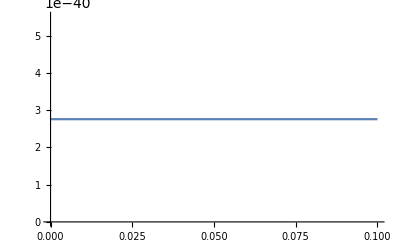

```mathematica
Plot[fb2[x,0,2.4]-fb1[x,0,2.4],{x,0,0.1}]
```

```mathematica
Re[EV[0.05,π/4,3]-EA[0.05,π/4,3]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.6885 and 0.00107655 for the integral and error estimates.

-3.6885

```mathematica
EVL
```

{0.979128,2.93386,2.82863,2.72956,2.58426,2.51632,2.42095,2.34278,2.28052,2.19875,2.11804,2.29243,2.22607,2.14711,2.06766,1.99161,1.93001,1.85168,1.79797,1.74728,1.69126,1.63224,1.77679,1.72907,1.66993,1.61069,1.55795,1.50841,1.45796,1.41397,1.37229,1.3094,1.26812,1.44757,1.41029,1.36467,1.32119,1.27208,1.23446,1.19632,1.16092,1.12552,1.08732,1.04892,1.2375,1.2099,1.17111,1.13164,1.09204,1.05832,1.02704,0.996793,0.96784,0.934495,0.90483,1.1161,1.09137,1.05637,1.02305,0.989451,0.959199,0.932688,0.906531,0.8844,0.856676,0.829443,1.0509,1.02856,0.994638,0.965927,0.938007,0.911717,0.887232,0.864734,0.843363,0.817825,0.792976,1.01766,0.997022,0.96692,0.938585,0.912359,0.886748,0.864526,0.844149,0.824571,0.799161,0.775861,1.00401,0.983621,0.954232,0.926852,0.90154,0.876797,0.854607,0.832927,0.816617,0.791853,0.769378,0.994087,0.97601,0.95065,0.923064,0.898033,0.875217,0.851945,0.831095,0.815177,0.790706,0.768423,0.99387,0.975854,0.950674,0.922644,0.897944,0.874967,0.851859,0.831065,0.815148,0.790725,0.768423,4.45069,4.20903,4.01941,3.8735,3.76906,3.43618,3.23925,3.09769,3.15044,2.85482,2.68587,2.80167,2.71415,2.61887,2.51735,2.38688,2.26775,2.18945,2.109,2.03452,1.9611,1.89574,1.94494,1.8948,1.83611,1.7777,1.7179,1.65342,1.60038,1.53612,1.49198,1.42864,1.38902,1.48758,1.44994,1.40604,1.35875,1.31319,1.26407,1.22204,1.18232,1.14499,1.10535,1.07002,1.23186,1.21162,1.17535,1.14032,1.10492,1.06022,1.02368,0.989129,0.962415,0.932886,0.90508,1.09371,1.07759,1.06719,1.03643,1.00536,0.962302,0.936511,0.900088,0.877422,0.852445,0.829636,1.04598,1.03406,1.00815,0.979282,0.949016,0.913232,0.889736,0.856752,0.835908,0.810508,0.790712,1.01731,1.00333,0.981097,0.953578,0.926857,0.889949,0.867778,0.83648,0.821505,0.797933,0.778486,0.998651,0.986802,0.96614,0.940114,0.912805,0.879105,0.858953,0.835921,0.81606,0.793068,0.774196,0.99574,0.983671,0.963677,0.938046,0.911732,0.878065,0.858104,0.834993,0.815397,0.792581,0.77378,0.995409,0.983404,0.963487,0.937942,0.911535,0.877863,0.857922,0.834993,0.815395,0.792581,0.773764,5.46332,5.49041,5.51865,5.54699,5.57695,5.61221,5.63841,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,3.40307,3.20811,3.05958,2.92666,2.82991,2.70902,2.59827,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,2.12742,2.05047,1.96646,1.89747,1.83877,1.76495,1.71055,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,1.52791,1.47723,1.42736,1.37476,1.33184,1.27461,1.23467,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,1.24813,1.19838,1.16597,1.13097,1.10152,1.06635,1.0247,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,1.114,1.07873,1.04719,1.01661,0.987979,0.954432,0.933828,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,1.04586,1.01917,0.988473,0.961388,0.936587,0.906794,0.884074,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,1.00196,0.978366,0.952054,0.92872,0.905355,0.878342,0.85839,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,0.99501,0.969571,0.942763,0.919755,0.89907,0.871403,0.852791,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,0.992996,0.96827,0.941603,0.91885,0.898315,0.87061,0.852511,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,0.992964,0.968245,0.941603,0.918795,0.898264,0.870594,0.852443,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40,-2.75818×10^-40}

```mathematica
E1=EV[2,0,0]
```

$Aborted

```mathematica
R=1;
E1=EV[0.05,0.001,3]
```

-2.75818×10^-40+2.36591×10^-39 ⅈ

```mathematica
4
```

```mathematica
L=0
VOL=NIntegrate[BelowCyl[1,0,x,y,z,0,R],{x,-L-2R,L+2R},{y,-L-2R,L+2R},{z,-L-R,L+R}];
```

0

```mathematica
BelowCyl[0.01,π/4,0,0,-0.02,3,R]
```

0

```mathematica
R=1;
L=3;
VOL=NIntegrate[BelowCyl[0.05,π/2,x,y,z,L,R],{x,-2L-2R,2L+2R},{y,-2L-2R,2L+2R},{z,-2L-2R,2L+2R},AccuracyGoal->5]
```

0.00772366

```mathematica
4*π/6.
```

2.0944

```mathematica
3*π+4*π/3.
```

13.6136

```mathematica
RR=ImplicitRegion[InCyl[h,t,x,y,0,L,2R]==1,{x,y}];
SA=NIntegrate[1.0,{x,y}∈RR,Method->{Automatic,"SymbolicProcessing"->0}];
```

```mathematica
BelowCyl[h_,t_,x_,y_,z_,L_,R_]:=(
hv={0,0,1-h};
xv={x,y,z};
dv=xv-hv;
rv={Cos[t],0,Sin[t]};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(
(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R)
)
&&z<0,1,0]
);
R=1;
L=3;
VOL=NIntegrate[BelowCyl[0.05,(π/2)/10.0,x,y,z,L,R],{x,-2L-2R,2L+2R},{y,-R,R},{z,-2R,0},AccuracyGoal->5,MinRecursion->100,MaxRecursion->1000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00775292 and 0.0000843516 for the integral and error estimates.

0.00775292

```mathematica
NIntegrate[BelowCyl[0.05,π/4,0,0.02,z,L,R],{z,-0.05,0.05}]
```

NORM: 0.63671

NORM: √(0.0004+Abs[-0.95+z]^2) √(1-(0.+(-0.95+z)/(√2))^2/(0.0004+Abs[-0.95+z]^2))

0.0498

```mathematica
Table[NIntegrate[BelowCyl[0.05,t,x,y,z,L,R],{x,-L-R,L+R},{y,-R,R},{z,-0.1,0},AccuracyGoal->20,MinRecursion->900,MaxRecursion->1000],{t,0,π/4,π/20.}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00801271 and 0.00012439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00769527 and 0.000117884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00769527 and 0.000117884 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

{0.0704922,0.00801271,0.00769527,0.00769527,0.00769527,0.00769527}

```mathematica
Table[t,{t,0,π/2,π/20.}]
```

{0.,0.15708,0.314159,0.471239,0.628319,0.785398,0.942478,1.09956,1.25664,1.41372,1.5708}

```mathematica
T=%
```

{0.0704922,0.00802087,0.00769139,0.00769139,0.00769139,0.00769139,0.00772308,0.00769139,0.00772308,0.00772308,0.00772308}

```mathematica
B=Table[t,{t,0,π/2,π/20.}]
```

{0.,0.15708,0.314159,0.471239,0.628319,0.785398,0.942478,1.09956,1.25664,1.41372,1.5708}

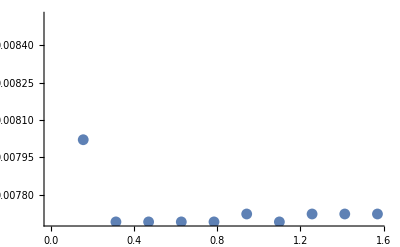

```mathematica
ListPlot[Transpose[{B,T}]]
```

```mathematica
Transpose[{T,B}]
```

{{0.0704922,0.},{0.00775292,0.15708},{0.00747245,0.314159},{0.00747245,0.471239},{0.00747245,0.628319},{0.00747245,0.785398},{0.00747245,0.942478},{0.00747245,1.09956},{0.00772308,1.25664},{0.00747245,1.41372},{0.00772308,1.5708}}

```mathematica
ArcCos[1-0.05]
```

0.31756